```mathematica
Clear["Global`*"];
acc=10;
steps=1000000;
(*--------------------------------------------*)
epsilon=0.1; ω=3;  l0=1; g=1;
deq1=x1'[t]==x2[t]
deq2=x2'[t]== -(g/(l0+epsilon*Sin[ω t]))*Sin[ x1[t]]
Tsection=2 π/ω
data={};
(*--------------------------------------------*)
```

x1'[t]==x2[t]

x2'[t]==-Sin[x1[t]]/(1+0.1 Sin[3 t])

(2 π)/3

```mathematica
x10=Pi;  
 x20=0;    (* sep x1-0, x2-1.772 *)
tmax=5000;
sol=NDSolve[{deq1,deq2,x1[0]==x10,x2[0]==x20},{x1,x2},{t,0,tmax},AccuracyGoal->acc, PrecisionGoal->acc,MaxSteps->steps];
xt1=x1/.sol[[1]]; xt2=x2/.sol[[1]];
(* Poincare - tt : time increased by 2π , n1 : number of points *)
tt=0; nl=0;  While[tt<tmax,AppendTo[data,{Mod[xt1[tt]+Pi, 2 Pi]-Pi,xt2[tt]}]; nl=nl+1; tt=tt+Tsection;]
Print["Last points = ", nl," Total points = ",Length[data]]
```

Last points = 23874 Total points = 23874

Last points = 2388 Total points = 2388

Last points = 2388 Total points = 2388

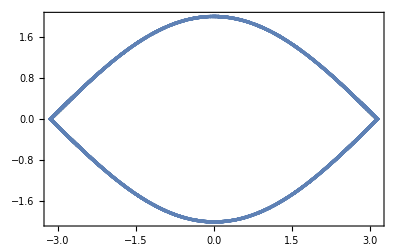

```mathematica
ListPlot[data,Frame->True,PlotRange->All,PlotStyle->PointSize[0.006]]
```

```mathematica
data=Drop[data,-nl];
```

```mathematica
data={}    (* delete all points *)
```

{}

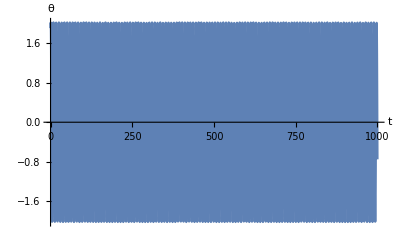

```mathematica
Plot[xt1[t],{t,0, tmax}, AxesLabel->{"t","θ"}]
```

x1'[t]==x2[t]

x2'[t]==-Sin[x1[t]]/(1+0.1 Sin[3 t])

{{x1→InterpolatingFunction[{{0., 1000.}}, <>],x2→InterpolatingFunction[{{0., 1000.}}, <>],x3→InterpolatingFunction[{{0., 1000.}}, <>],x4→InterpolatingFunction[{{0., 1000.}}, <>]}}

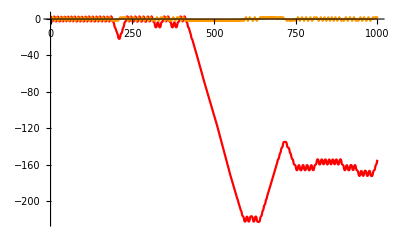

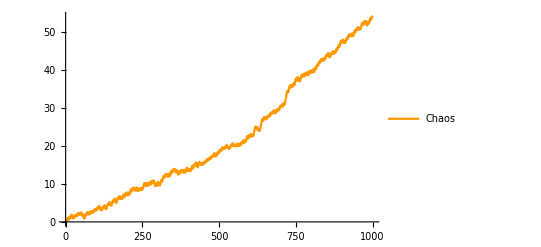

```mathematica
(*FLI*)
x10=2.6;  
 x20=0.2;  
tmax=1000;
deq1=x1'[t]==x2[t]
deq2=x2'[t]== -(g/(l0+epsilon*Sin[ω t]))*Sin[ x1[t]]
deq3=x3'[t]==x4[t];
deq4=x4'[t]==-(g/(l0+epsilon*Sin[ω t]))*Cos[ x1[t]]*x3[t];
sol=NDSolve[{deq1,deq2,deq3,deq4,x1[0]==x10,x2[0]==x20,x3[0]==1, x4[0]==0}, {x1,x2,x3,x4},{t,0,tmax},AccuracyGoal->acc, PrecisionGoal->acc,MaxSteps->steps]
xt1=x1[t]/.sol[[1]]; 
xt2=x2[t]/.sol[[1]];
xt3=x3[t]/.sol[[1]];
xt4=x4[t]/.sol[[1]];
Plot[{xt1,xt2},{t,0,tmax},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0.6,0]}]
FLI[t_]=Log[10,xt3^2+xt4^2]/2;
graph1=Plot[Evaluate[FLI[t]],{t,0,tmax}, PlotRange->All,PlotStyle->RGBColor[1,0.6,0],PlotLegends->LineLegend[{RGBColor[1,0.6,0]},{"Chaos"}]]
```

x1'[t]==x2[t]

x2'[t]==-Sin[x1[t]]/(1+0.1 Sin[3 t])

{{x1→InterpolatingFunction[{{0., 1000.}}, <>],x2→InterpolatingFunction[{{0., 1000.}}, <>],x3→InterpolatingFunction[{{0., 1000.}}, <>],x4→InterpolatingFunction[{{0., 1000.}}, <>]}}

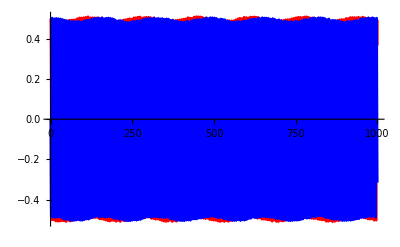

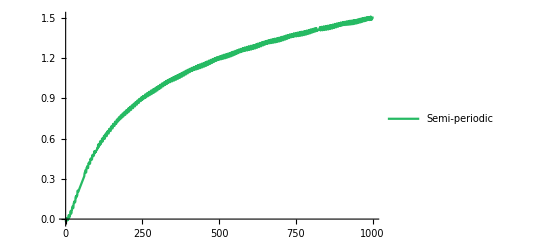

```mathematica
x10=2.6;  
 x20=0.2;  
tmax=1000;
deq1=x1'[t]==x2[t]
deq2=x2'[t]== -(g/(l0+epsilon*Sin[ω t]))*Sin[ x1[t]]
deq3=x3'[t]==x4[t];
deq4=x4'[t]==-(g/(l0+epsilon*Sin[ω t]))*Cos[ x1[t]]*x3[t];
sol=NDSolve[{deq1,deq2,deq3,deq4,x1[0]==x10,x2[0]==x20,x3[0]==1, x4[0]==0}, {x1,x2,x3,x4},{t,0,tmax},AccuracyGoal->acc, PrecisionGoal->acc,MaxSteps->steps]
xt1=x1[t]/.sol[[1]]; 
xt2=x2[t]/.sol[[1]];
xt3=x3[t]/.sol[[1]];
xt4=x4[t]/.sol[[1]];
Plot[{xt1,xt2},{t,0,tmax},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
FLI[t_]=Log[10,xt3^2+xt4^2]/2;
graph2=Plot[Evaluate[FLI[t]],{t,0,tmax}, PlotRange->All,PlotStyle->RGBColor[0.15,0.73,0.39],PlotLegends->LineLegend[{RGBColor[0.15,0.73,0.39]},{"Semi-periodic"}]]
```

x1'[t]==x2[t]

x2'[t]==-Sin[x1[t]]/(1+0.1 Sin[3 t])

{{x1→InterpolatingFunction[{{0., 1000.}}, <>],x2→InterpolatingFunction[{{0., 1000.}}, <>],x3→InterpolatingFunction[{{0., 1000.}}, <>],x4→InterpolatingFunction[{{0., 1000.}}, <>]}}

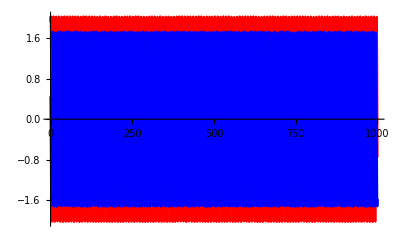

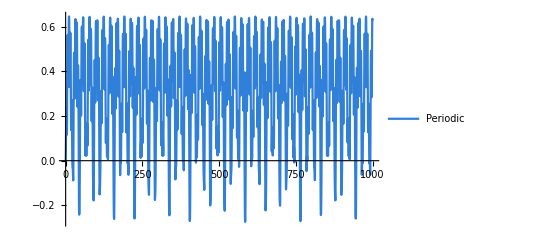

```mathematica
x10=1.90845;  
 x20=0.4508;  
tmax=1000;
deq1=x1'[t]==x2[t]
deq2=x2'[t]== -(g/(l0+epsilon*Sin[ω t]))*Sin[ x1[t]]
deq3=x3'[t]==x4[t];
deq4=x4'[t]==-(g/(l0+epsilon*Sin[ω t]))*Cos[ x1[t]]*x3[t];
sol=NDSolve[{deq1,deq2,deq3,deq4,x1[0]==x10,x2[0]==x20,x3[0]==1, x4[0]==0}, {x1,x2,x3,x4},{t,0,tmax},AccuracyGoal->acc, PrecisionGoal->acc,MaxSteps->steps]
xt1=x1[t]/.sol[[1]]; 
xt2=x2[t]/.sol[[1]];
xt3=x3[t]/.sol[[1]];
xt4=x4[t]/.sol[[1]];
Plot[{xt1,xt2},{t,0,tmax},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
FLI[t_]=Log[10,xt3^2+xt4^2]/2;
graph3=Plot[Evaluate[FLI[t]],{t,0,tmax}, PlotRange->All,PlotStyle->RGBColor[0.19,0.5,0.85],PlotLegends->LineLegend[{RGBColor[0.19,0.5,0.85]},{"Periodic"}]]
```

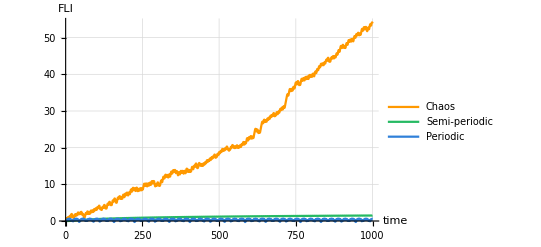

```mathematica
Show[{graph1,graph2,graph3}, AxesLabel->{"time","FLI"},GridLines->Automatic]
```

```mathematica
(*LCN*)
deq1=x1'[t]==x2[t]
deq2=x2'[t]== -(g/(l0+epsilon*Sin[ω t]))*Sin[ x1[t]]
```

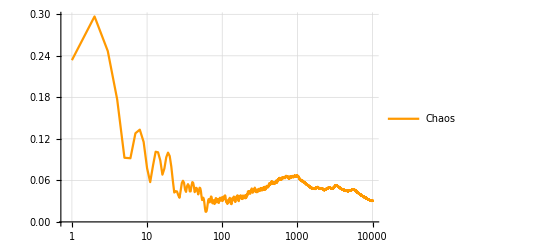

```mathematica
dataplot = Import["C:\\Users\\retse\\Desktop\\lce_chaos.txt",{"Data"}];
fig1=ListLogLinearPlot[dataplot,PlotRange->All, Joined->True,PlotStyle->RGBColor[1,0.6,0],PlotLegends->LineLegend[{RGBColor[1,0.6,0]},{"Chaos"}],GridLines->Automatic]
```

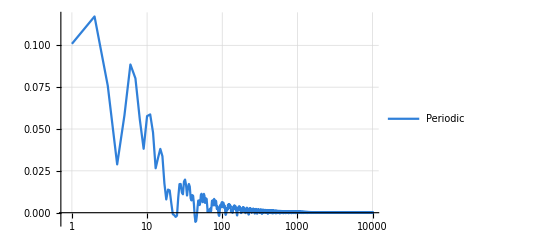

```mathematica
dataplot = Import["C:\\Users\\retse\\Desktop\\lce_periodic.txt",{"Data"}];
fig2=ListLogLinearPlot[dataplot,PlotRange->All, Joined->True,PlotStyle->RGBColor[0.19,0.5,0.85],PlotLegends->LineLegend[{RGBColor[0.19,0.5,0.85]},{"Periodic"}],GridLines->Automatic]
```

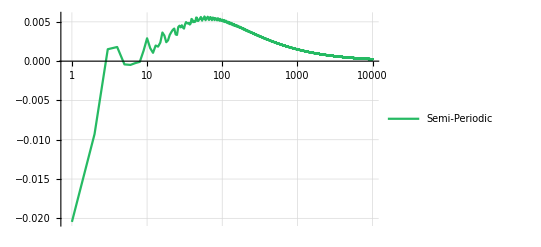

```mathematica
dataplot = Import["C:\\Users\\retse\\Desktop\\lce_semi.txt",{"Data"}];
fig3=ListLogLinearPlot[dataplot,PlotRange->All, Joined->True,PlotStyle->RGBColor[0.15,0.73,0.39],PlotLegends->LineLegend[{RGBColor[0.15,0.73,0.39]},{"Semi-Periodic"}],GridLines->Automatic]
```

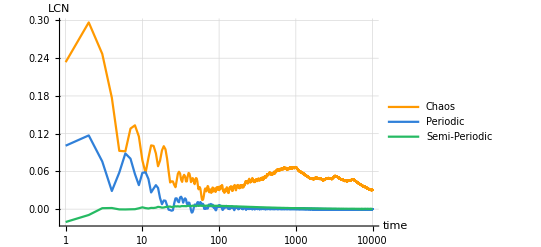

```mathematica
Show[{fig1,fig2,fig3}, AxesLabel->{"time","LCN"},PlotRange->All,GridLines->Automatic]
```